```mathematica
Integrate[Exp[-1/2x^2-a x^4],{x,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(1/32/a) BesselK[1/4,1/(32 a)])/(2 √2 √a),Re[a]>0]

```mathematica
Integrate[x^# Exp[-1/2x^2-a x^4],{x,-Infinity,Infinity}]&/@{0,2,4}
```

{ConditionalExpression[(ⅇ^(1/32/a) BesselK[1/4,1/(32 a)])/(2 √2 √a),Re[a]>0],ConditionalExpression[(ⅇ^(1/32/a) π (-BesselI[-1/4,1/(32 a)]+(1+16 a) BesselI[1/4,1/(32 a)]-BesselI[3/4,1/(32 a)]+BesselI[5/4,1/(32 a)]))/(32 a^(3/2)),Re[a]>0],ConditionalExpression[(ⅇ^(1/32/a) ((1+8 a) BesselK[1/4,1/(32 a)]-BesselK[3/4,1/(32 a)]))/(64 √2 a^(5/2)),Re[a]>0]}

```mathematica
{i0,i2,i4}=%2[[;;,1]]
```

{(ⅇ^(1/32/a) BesselK[1/4,1/(32 a)])/(2 √2 √a),(ⅇ^(1/32/a) π (-BesselI[-1/4,1/(32 a)]+(1+16 a) BesselI[1/4,1/(32 a)]-BesselI[3/4,1/(32 a)]+BesselI[5/4,1/(32 a)]))/(32 a^(3/2)),(ⅇ^(1/32/a) ((1+8 a) BesselK[1/4,1/(32 a)]-BesselK[3/4,1/(32 a)]))/(64 √2 a^(5/2))}

```mathematica
m2=FullSimplify[i2/i0]
m4=FullSimplify[i4/i0]
```

(π (-BesselI[-1/4,1/(32 a)]+(1+16 a) BesselI[1/4,1/(32 a)]-BesselI[3/4,1/(32 a)]+BesselI[5/4,1/(32 a)]))/(8 √2 a BesselK[1/4,1/(32 a)])

(1+8 a-BesselK[3/4,1/(32 a)]/BesselK[1/4,1/(32 a)])/(32 a^2)

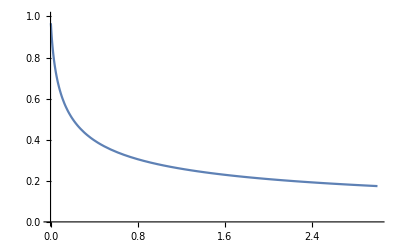

```mathematica
Plot[m2,{a,.003,3},PlotRange->{0,1}]
```

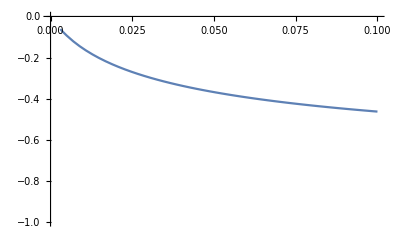

```mathematica
Plot[m4/m2^2-3,{a,.003,.1},PlotRange->{-1,0}]
```

```mathematica
m4/m2^2-3/.a->.01
```

-0.156782

```mathematica
Integrate[x^# Exp[-x^4],{x,-Infinity,Infinity}]&/@{0,2,4}
```

{2 Gamma[5/4],1/2 Gamma[3/4],1/2 Gamma[5/4]}

```mathematica
%[[3]]/%[[2]]^2*%[[1]]
```

(4 Gamma[5/4]^2)/Gamma[3/4]^2

```mathematica
%//FullSimplify
```

(4 Gamma[5/4]^2)/Gamma[3/4]^2

```mathematica
%//N
```

2.18844

```mathematica
3-%
```

0.81156

```mathematica
3-%34//FullSimplify
```

3-(4 Gamma[5/4]^2)/Gamma[3/4]^2

```mathematica
m4/m2^2/.a->10000.
```

2.18983